## Some definitions first

```mathematica
allGraphs=allGraphs6;
```

```mathematica
realyNullAtomKeys=allGraphs6NullAtomKeys;
```

```mathematica
IsRefinement[sets1_,sets2_]:=Block[{sets,result=False,merged},
sets=Subsets[sets2,{2}];
Table[
merged=Sort[Join[s[[1]],s[[2]]]];
If[MemberQ[sets1,merged],
result=True
(*Print["Not member",merged, " from ",sets1]*)
]
,
{s,sets}];
result
]
```

```mathematica
MobiusGraph[key_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[to[[1]],from[[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
MobiusTable[key_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars,result=Association[],set,level},
vars=ListofVars[form];
Table[
level=StringCount[SymbolName[n],"x"];
If[KeyExistsQ[result,level],
set=result[level],
set={}
];
set=Append[set,Coefficient[form,n]];
result[level]=set
,{n,vars}];
result
]
```

## Inequalities so we have pairs

```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

53071

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqs2=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

53071

```mathematica
ineqs2
```

{n1x2x3x4x5x6>0,-n12x3x4x5x6+n1x2x3x4x5x6>0,n123x4x5x6-n12x3x4x5x6-n13x2x4x5x6+n1x2x3x4x5x6>0,-n1234x5x6+n123x4x5x6+n124x3x5x6-n12x3x4x5x6+n134x2x5x6-n13x2x4x5x6-n14x2x3x5x6+n1x2x3x4x5x6>0,n12345x6-n1234x5x6-n1235x4x6+n123x4x5x6-n1245x3x6+n124x3x5x6+n125x3x4x6-n12x3x4x5x6-n1345x2x6+n134x2x5x6+n135x2x4x6-n13x2x4x5x6+n145x2x3x6-n14x2x3x5x6-n15x2x3x4x6+n1x2x3x4x5x6>0,53061,-n1x2x3x46x5+n1x2x3x4x5x6>0,n1x2x3x456-n1x2x3x46x5-n1x2x3x4x56+n1x2x3x4x5x6>0,n1x2x3x46x5>0,-n1x2x3x4x56+n1x2x3x4x5x6>0,n1x2x3x4x56>0}
 |  |  |  |

```mathematica
realnullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofourrealnull"],0],{k,realyNullAtomKeys}];Length[realnullAtomFacts]
```

203

```mathematica
ineqsW2=Monitor[Simplify[Fold[And,Select[ineqs2,Length[ListofVars[#]]==2&]],Trig->False,ComplexityFunction->MyLeafCount],countDone];Length[ineqsW2]
```

856

```mathematica
Length[allGraphs]
```

53071

```mathematica
allGraphs[9,"colofourrealnull"]
```

-n1x2x3x45x6+n1x2x3x4x5x6

```mathematica
BaseVarComp[v1_,v2_]:=Block[{s1,s2,l1,l2},
s1=SymbolName[v1];
s2=SymbolName[v2];
l1=StringCount[s1,"x"];
l2=StringCount[s2,"x"];
If[l1≠l2,
l1<l2,
s1<s2
]
]
```

```mathematica
BaseVarComp[n123456,n12345x6]
```

True

```mathematica
vars2=Sort[ListofVars[Select[ineqsW2,Length[ListofVars[#]]==2&]],BaseVarComp]//DeleteDuplicates
```

{n123456,n12345x6,n12346x5,n1234x56,n12356x4,n1235x46,n1236x45,n123x456,n12456x3,n1245x36,n1246x35,n124x356,n1256x34,n125x346,n126x345,n12x3456,n13456x2,n1345x26,n1346x25,n134x256,n1356x24,n135x246,n136x245,n13x2456,n1456x23,n145x236,n146x235,n14x2356,n156x234,n15x2346,n16x2345,n1x23456,n1234x5x6,n1235x4x6,n123x45x6,n1245x3x6,n124x35x6,n125x34x6,n12x345x6,n1345x2x6,n134x25x6,n135x24x6,n13x245x6,n145x23x6,n14x235x6,n15x234x6,n1x2345x6,n1236x4x5,n123x46x5,n1246x3x5,n124x36x5,n126x34x5,n12x346x5,n1346x2x5,n134x26x5,n136x24x5,n13x246x5,n146x23x5,n14x236x5,n16x234x5,n1x2346x5,n123x4x56,n124x3x56,n12x34x56,n134x2x56,n13x24x56,n14x23x56,n1x234x56,n1256x3x4,n125x36x4,n126x35x4,n12x356x4,n1356x2x4,n135x26x4,n136x25x4,n13x256x4,n156x23x4,n15x236x4,n16x235x4,n1x2356x4,n125x3x46,n12x35x46,n135x2x46,n13x25x46,n15x23x46,n1x235x46,n126x3x45,n12x36x45,n136x2x45,n13x26x45,n16x23x45,n1x236x45,n12x3x456,n13x2x456,n1x23x456,n1456x2x3,n145x26x3,n146x25x3,n14x256x3,n156x24x3,n15x246x3,n16x245x3,n1x2456x3,n145x2x36,n14x25x36,n15x24x36,n1x245x36,n146x2x35,n14x26x35,n16x24x35,n1x246x35,n14x2x356,n1x24x356,n156x2x34,n15x26x34,n16x25x34,n1x256x34,n15x2x346,n1x25x346,n16x2x345,n1x26x345,n1x2x3456,n123x4x5x6,n124x3x5x6,n12x34x5x6,n134x2x5x6,n13x24x5x6,n14x23x5x6,n1x234x5x6,n125x3x4x6,n12x35x4x6,n135x2x4x6,n13x25x4x6,n15x23x4x6,n1x235x4x6,n126x3x4x5,n12x36x4x5,n136x2x4x5,n13x26x4x5,n16x23x4x5,n1x236x4x5,n12x3x45x6,n13x2x45x6,n1x23x45x6,n12x3x46x5,n13x2x46x5,n1x23x46x5,n12x3x4x56,n13x2x4x56,n1x23x4x56,n145x2x3x6,n14x25x3x6,n15x24x3x6,n1x245x3x6,n146x2x3x5,n14x26x3x5,n16x24x3x5,n1x246x3x5,n14x2x35x6,n1x24x35x6,n14x2x36x5,n1x24x36x5,n14x2x3x56,n1x24x3x56,n156x2x3x4,n15x26x3x4,n16x25x3x4,n1x256x3x4,n15x2x34x6,n1x25x34x6,n15x2x36x4,n1x25x36x4,n15x2x3x46,n1x25x3x46,n16x2x34x5,n1x26x34x5,n16x2x35x4,n1x26x35x4,n16x2x3x45,n1x26x3x45,n1x2x345x6,n1x2x346x5,n1x2x34x56,n1x2x356x4,n1x2x35x46,n1x2x36x45,n1x2x3x456,n12x3x4x5x6,n13x2x4x5x6,n1x23x4x5x6,n14x2x3x5x6,n1x24x3x5x6,n15x2x3x4x6,n1x25x3x4x6,n16x2x3x4x5,n1x26x3x4x5,n1x2x34x5x6,n1x2x35x4x6,n1x2x36x4x5,n1x2x3x45x6,n1x2x3x46x5,n1x2x3x4x56,n1x2x3x4x5x6}

```mathematica
InverseNull[symbol_]:=First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==symbol&]]
```

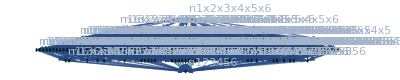

```mathematica
partialOrder=Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[k->Labeled[allGraphs[InverseNull[k],"graph"],k],{k,vars2}],GraphLayout->"LayeredDigraphEmbedding", VertexStyle->Table[k->ColourForKey[allGraphs,InverseNull[k]],{k,vars2}]]
```

```mathematica
EdgeCount[partialOrder]
```

856

```mathematica
VertexCount[partialOrder]
```

203

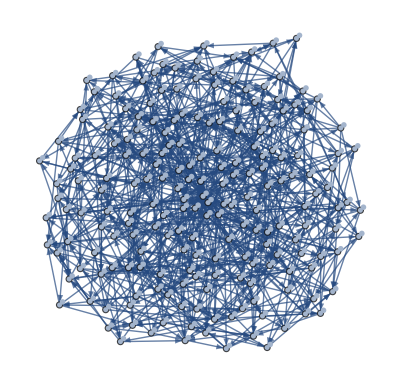

```mathematica
Graph[Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"graph"],{k,realyNullAtomKeys}],MemberQ[vars2,#[[1]]]&]]
```

```mathematica
Take[ineqsW,5]
```

Take::normal: Nonatomic expression expected at position 1 in Take[ineqsW,5].

Take[ineqsW,5]

```mathematica
pairs=Subsets[nullAtomSymbols,{2}];Length[pairs]
```

Subsets::normal: Nonatomic expression expected at position 1 in Subsets[nullAtomSymbols,{2}].

2

```mathematica
Take[nullAtomFacts,3]
```

Take::normal: Nonatomic expression expected at position 1 in Take[nullAtomFacts,3].

Take[nullAtomFacts,3]

```mathematica
atomFactsAnd=Fold[And,nullAtomFacts]
```

Fold::normal: Nonatomic expression expected at position 2 in Fold[And,nullAtomFacts].

Fold[And,nullAtomFacts]

```mathematica
allGraphs[6562,"graph"]
```

-Graphics-

## Mobius and zeta

```mathematica
allVars=Sort[Map[First,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]]]
```

{n12345x6,n12346x5,n1234x56,n1234x5x6,n1234x5x6,n1234x5x6,n12356x4,n1235x46,n1235x4x6,n1235x4x6,n1235x4x6,n1236x45,n1236x4x5,n1236x4x5,n1236x4x5,n123x456,n123x45x6,n123x45x6,n123x45x6,n123x46x5,n123x46x5,n123x46x5,n123x4x56,n123x4x56,n123x4x56,n123x4x5x6,n123x4x5x6,n123x4x5x6,n123x4x5x6,n123x4x5x6,n123x4x5x6,n12456x3,n1245x36,n1245x3x6,n1245x3x6,n1245x3x6,n1246x35,n1246x3x5,n1246x3x5,n1246x3x5,n124x356,n124x35x6,n124x35x6,n124x35x6,n124x36x5,n124x36x5,n124x36x5,n124x3x56,n124x3x56,n124x3x56,n124x3x5x6,n124x3x5x6,n124x3x5x6,n124x3x5x6,n124x3x5x6,n124x3x5x6,n1256x34,n1256x3x4,n1256x3x4,n1256x3x4,n125x346,n125x34x6,n125x34x6,n125x34x6,n125x36x4,n125x36x4,n125x36x4,n125x3x46,n125x3x46,n125x3x46,n125x3x4x6,n125x3x4x6,n125x3x4x6,n125x3x4x6,n125x3x4x6,n125x3x4x6,n126x345,n126x34x5,n126x34x5,n126x34x5,n126x35x4,n126x35x4,n126x35x4,n126x3x45,n126x3x45,n126x3x45,n126x3x4x5,n126x3x4x5,n126x3x4x5,n126x3x4x5,n126x3x4x5,n126x3x4x5,n12x3456,n12x345x6,n12x345x6,n12x345x6,n12x346x5,n12x346x5,n12x346x5,n12x34x56,n12x34x56,n12x34x56,n12x34x5x6,n12x34x5x6,n12x34x5x6,n12x34x5x6,n12x34x5x6,n12x34x5x6,n12x356x4,n12x356x4,n12x356x4,n12x35x46,n12x35x46,n12x35x46,n12x35x4x6,n12x35x4x6,n12x35x4x6,n12x35x4x6,n12x35x4x6,n12x35x4x6,n12x36x45,n12x36x45,n12x36x45,n12x36x4x5,n12x36x4x5,n12x36x4x5,n12x36x4x5,n12x36x4x5,n12x36x4x5,n12x3x456,n12x3x456,n12x3x456,n12x3x45x6,n12x3x45x6,n12x3x45x6,n12x3x45x6,n12x3x45x6,n12x3x45x6,n12x3x46x5,n12x3x46x5,n12x3x46x5,n12x3x46x5,n12x3x46x5,n12x3x46x5,n12x3x4x56,n12x3x4x56,n12x3x4x56,n12x3x4x56,n12x3x4x56,n12x3x4x56,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n13456x2,n1345x26,n1345x2x6,n1345x2x6,n1345x2x6,n1346x25,n1346x2x5,n1346x2x5,n1346x2x5,n134x256,n134x25x6,n134x25x6,n134x25x6,n134x26x5,n134x26x5,n134x26x5,n134x2x56,n134x2x56,n134x2x56,n134x2x5x6,n134x2x5x6,n134x2x5x6,n134x2x5x6,n134x2x5x6,n134x2x5x6,n1356x24,n1356x2x4,n1356x2x4,n1356x2x4,n135x246,n135x24x6,n135x24x6,n135x24x6,n135x26x4,n135x26x4,n135x26x4,n135x2x46,n135x2x46,n135x2x46,n135x2x4x6,n135x2x4x6,n135x2x4x6,n135x2x4x6,n135x2x4x6,n135x2x4x6,n136x245,n136x24x5,n136x24x5,n136x24x5,n136x25x4,n136x25x4,n136x25x4,n136x2x45,n136x2x45,n136x2x45,n136x2x4x5,n136x2x4x5,n136x2x4x5,n136x2x4x5,n136x2x4x5,n136x2x4x5,n13x2456,n13x245x6,n13x245x6,n13x245x6,n13x246x5,n13x246x5,n13x246x5,n13x24x56,n13x24x56,n13x24x56,n13x24x5x6,n13x24x5x6,n13x24x5x6,n13x24x5x6,n13x24x5x6,n13x24x5x6,n13x256x4,n13x256x4,n13x256x4,n13x25x46,n13x25x46,n13x25x46,n13x25x4x6,n13x25x4x6,n13x25x4x6,n13x25x4x6,n13x25x4x6,n13x25x4x6,n13x26x45,n13x26x45,n13x26x45,n13x26x4x5,n13x26x4x5,n13x26x4x5,n13x26x4x5,n13x26x4x5,n13x26x4x5,n13x2x456,n13x2x456,n13x2x456,n13x2x45x6,n13x2x45x6,n13x2x45x6,n13x2x45x6,n13x2x45x6,n13x2x45x6,n13x2x46x5,n13x2x46x5,n13x2x46x5,n13x2x46x5,n13x2x46x5,n13x2x46x5,n13x2x4x56,n13x2x4x56,n13x2x4x56,n13x2x4x56,n13x2x4x56,n13x2x4x56,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n1456x23,n1456x2x3,n1456x2x3,n1456x2x3,n145x236,n145x23x6,n145x23x6,n145x23x6,n145x26x3,n145x26x3,n145x26x3,n145x2x36,n145x2x36,n145x2x36,n145x2x3x6,n145x2x3x6,n145x2x3x6,n145x2x3x6,n145x2x3x6,n145x2x3x6,n146x235,n146x23x5,n146x23x5,n146x23x5,n146x25x3,n146x25x3,n146x25x3,n146x2x35,n146x2x35,n146x2x35,n146x2x3x5,n146x2x3x5,n146x2x3x5,n146x2x3x5,n146x2x3x5,n146x2x3x5,n14x2356,n14x235x6,n14x235x6,n14x235x6,n14x236x5,n14x236x5,n14x236x5,n14x23x56,n14x23x56,n14x23x56,n14x23x5x6,n14x23x5x6,n14x23x5x6,n14x23x5x6,n14x23x5x6,n14x23x5x6,n14x256x3,n14x256x3,n14x256x3,n14x25x36,n14x25x36,n14x25x36,n14x25x3x6,n14x25x3x6,n14x25x3x6,n14x25x3x6,n14x25x3x6,n14x25x3x6,n14x26x35,n14x26x35,n14x26x35,n14x26x3x5,n14x26x3x5,n14x26x3x5,n14x26x3x5,n14x26x3x5,n14x26x3x5,n14x2x356,n14x2x356,n14x2x356,n14x2x35x6,n14x2x35x6,n14x2x35x6,n14x2x35x6,n14x2x35x6,n14x2x35x6,n14x2x36x5,n14x2x36x5,n14x2x36x5,n14x2x36x5,n14x2x36x5,n14x2x36x5,n14x2x3x56,n14x2x3x56,n14x2x3x56,n14x2x3x56,n14x2x3x56,n14x2x3x56,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n156x234,n156x23x4,n156x23x4,n156x23x4,n156x24x3,n156x24x3,n156x24x3,n156x2x34,n156x2x34,n156x2x34,n156x2x3x4,n156x2x3x4,n156x2x3x4,n156x2x3x4,n156x2x3x4,n156x2x3x4,n15x2346,n15x234x6,n15x234x6,n15x234x6,n15x236x4,n15x236x4,n15x236x4,n15x23x46,n15x23x46,n15x23x46,n15x23x4x6,n15x23x4x6,n15x23x4x6,n15x23x4x6,n15x23x4x6,n15x23x4x6,n15x246x3,n15x246x3,n15x246x3,n15x24x36,n15x24x36,n15x24x36,n15x24x3x6,n15x24x3x6,n15x24x3x6,n15x24x3x6,n15x24x3x6,n15x24x3x6,n15x26x34,n15x26x34,n15x26x34,n15x26x3x4,n15x26x3x4,n15x26x3x4,n15x26x3x4,n15x26x3x4,n15x26x3x4,n15x2x346,n15x2x346,n15x2x346,n15x2x34x6,n15x2x34x6,n15x2x34x6,n15x2x34x6,n15x2x34x6,n15x2x34x6,n15x2x36x4,n15x2x36x4,n15x2x36x4,n15x2x36x4,n15x2x36x4,n15x2x36x4,n15x2x3x46,n15x2x3x46,n15x2x3x46,n15x2x3x46,n15x2x3x46,n15x2x3x46,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n16x2345,n16x234x5,n16x234x5,n16x234x5,n16x235x4,n16x235x4,n16x235x4,n16x23x45,n16x23x45,n16x23x45,n16x23x4x5,n16x23x4x5,n16x23x4x5,n16x23x4x5,n16x23x4x5,n16x23x4x5,n16x245x3,n16x245x3,n16x245x3,n16x24x35,n16x24x35,n16x24x35,n16x24x3x5,n16x24x3x5,n16x24x3x5,n16x24x3x5,n16x24x3x5,n16x24x3x5,n16x25x34,n16x25x34,n16x25x34,n16x25x3x4,n16x25x3x4,n16x25x3x4,n16x25x3x4,n16x25x3x4,n16x25x3x4,n16x2x345,n16x2x345,n16x2x345,n16x2x34x5,n16x2x34x5,n16x2x34x5,n16x2x34x5,n16x2x34x5,n16x2x34x5,n16x2x35x4,n16x2x35x4,n16x2x35x4,n16x2x35x4,n16x2x35x4,n16x2x35x4,n16x2x3x45,n16x2x3x45,n16x2x3x45,n16x2x3x45,n16x2x3x45,n16x2x3x45,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n1x23456,n1x2345x6,n1x2345x6,n1x2345x6,n1x2346x5,n1x2346x5,n1x2346x5,n1x234x56,n1x234x56,n1x234x56,n1x234x5x6,n1x234x5x6,n1x234x5x6,n1x234x5x6,n1x234x5x6,n1x234x5x6,n1x2356x4,n1x2356x4,n1x2356x4,n1x235x46,n1x235x46,n1x235x46,n1x235x4x6,n1x235x4x6,n1x235x4x6,n1x235x4x6,n1x235x4x6,n1x235x4x6,n1x236x45,n1x236x45,n1x236x45,n1x236x4x5,n1x236x4x5,n1x236x4x5,n1x236x4x5,n1x236x4x5,n1x236x4x5,n1x23x456,n1x23x456,n1x23x456,n1x23x45x6,n1x23x45x6,n1x23x45x6,n1x23x45x6,n1x23x45x6,n1x23x45x6,n1x23x46x5,n1x23x46x5,n1x23x46x5,n1x23x46x5,n1x23x46x5,n1x23x46x5,n1x23x4x56,n1x23x4x56,n1x23x4x56,n1x23x4x56,n1x23x4x56,n1x23x4x56,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x2456x3,n1x2456x3,n1x2456x3,n1x245x36,n1x245x36,n1x245x36,n1x245x3x6,n1x245x3x6,n1x245x3x6,n1x245x3x6,n1x245x3x6,n1x245x3x6,n1x246x35,n1x246x35,n1x246x35,n1x246x3x5,n1x246x3x5,n1x246x3x5,n1x246x3x5,n1x246x3x5,n1x246x3x5,n1x24x356,n1x24x356,n1x24x356,n1x24x35x6,n1x24x35x6,n1x24x35x6,n1x24x35x6,n1x24x35x6,n1x24x35x6,n1x24x36x5,n1x24x36x5,n1x24x36x5,n1x24x36x5,n1x24x36x5,n1x24x36x5,n1x24x3x56,n1x24x3x56,n1x24x3x56,n1x24x3x56,n1x24x3x56,n1x24x3x56,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x256x34,n1x256x34,n1x256x34,n1x256x3x4,n1x256x3x4,n1x256x3x4,n1x256x3x4,n1x256x3x4,n1x256x3x4,n1x25x346,n1x25x346,n1x25x346,n1x25x34x6,n1x25x34x6,n1x25x34x6,n1x25x34x6,n1x25x34x6,n1x25x34x6,n1x25x36x4,n1x25x36x4,n1x25x36x4,n1x25x36x4,n1x25x36x4,n1x25x36x4,n1x25x3x46,n1x25x3x46,n1x25x3x46,n1x25x3x46,n1x25x3x46,n1x25x3x46,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x26x345,n1x26x345,n1x26x345,n1x26x34x5,n1x26x34x5,n1x26x34x5,n1x26x34x5,n1x26x34x5,n1x26x34x5,n1x26x35x4,n1x26x35x4,n1x26x35x4,n1x26x35x4,n1x26x35x4,n1x26x35x4,n1x26x3x45,n1x26x3x45,n1x26x3x45,n1x26x3x45,n1x26x3x45,n1x26x3x45,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x2x3456,n1x2x3456,n1x2x3456,n1x2x345x6,n1x2x345x6,n1x2x345x6,n1x2x345x6,n1x2x345x6,n1x2x345x6,n1x2x346x5,n1x2x346x5,n1x2x346x5,n1x2x346x5,n1x2x346x5,n1x2x346x5,n1x2x34x56,n1x2x34x56,n1x2x34x56,n1x2x34x56,n1x2x34x56,n1x2x34x56,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x356x4,n1x2x356x4,n1x2x356x4,n1x2x356x4,n1x2x356x4,n1x2x356x4,n1x2x35x46,n1x2x35x46,n1x2x35x46,n1x2x35x46,n1x2x35x46,n1x2x35x46,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x36x45,n1x2x36x45,n1x2x36x45,n1x2x36x45,n1x2x36x45,n1x2x36x45,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x3x456,n1x2x3x456,n1x2x3x456,n1x2x3x456,n1x2x3x456,n1x2x3x456,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6}

```mathematica
Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==203&]
```

{7174453}

```mathematica
vertices=Sort[Sort[allVars],StringCount [SymbolName[#1],"x"]<StringCount [SymbolName[#2],"x"]&]
```

{n1x23456,n16x2345,n15x2346,n156x234,n14x2356,n146x235,n145x236,n1456x23,n13x2456,n136x245,n135x246,n1356x24,n134x256,n1346x25,n1345x26,n13456x2,n12x3456,n126x345,n125x346,n1256x34,n124x356,n1246x35,n1245x36,n12456x3,n123x456,n1236x45,n1235x46,n12356x4,n1234x56,n12346x5,n12345x6,n1x2x3456,n1x2x3456,n1x2x3456,n1x26x345,n1x26x345,n1x26x345,n1x25x346,n1x25x346,n1x25x346,n1x256x34,n1x256x34,n1x256x34,n1x24x356,n1x24x356,n1x24x356,n1x246x35,n1x246x35,n1x246x35,n1x245x36,n1x245x36,n1x245x36,n1x2456x3,n1x2456x3,n1x2456x3,n1x23x456,n1x23x456,n1x23x456,n1x236x45,n1x236x45,n1x236x45,n1x235x46,n1x235x46,n1x235x46,n1x2356x4,n1x2356x4,n1x2356x4,n1x234x56,n1x234x56,n1x234x56,n1x2346x5,n1x2346x5,n1x2346x5,n1x2345x6,n1x2345x6,n1x2345x6,n16x2x345,n16x2x345,n16x2x345,n16x25x34,n16x25x34,n16x25x34,n16x24x35,n16x24x35,n16x24x35,n16x245x3,n16x245x3,n16x245x3,n16x23x45,n16x23x45,n16x23x45,n16x235x4,n16x235x4,n16x235x4,n16x234x5,n16x234x5,n16x234x5,n15x2x346,n15x2x346,n15x2x346,n15x26x34,n15x26x34,n15x26x34,n15x24x36,n15x24x36,n15x24x36,n15x246x3,n15x246x3,n15x246x3,n15x23x46,n15x23x46,n15x23x46,n15x236x4,n15x236x4,n15x236x4,n15x234x6,n15x234x6,n15x234x6,n156x2x34,n156x2x34,n156x2x34,n156x24x3,n156x24x3,n156x24x3,n156x23x4,n156x23x4,n156x23x4,n14x2x356,n14x2x356,n14x2x356,n14x26x35,n14x26x35,n14x26x35,n14x25x36,n14x25x36,n14x25x36,n14x256x3,n14x256x3,n14x256x3,n14x23x56,n14x23x56,n14x23x56,n14x236x5,n14x236x5,n14x236x5,n14x235x6,n14x235x6,n14x235x6,n146x2x35,n146x2x35,n146x2x35,n146x25x3,n146x25x3,n146x25x3,n146x23x5,n146x23x5,n146x23x5,n145x2x36,n145x2x36,n145x2x36,n145x26x3,n145x26x3,n145x26x3,n145x23x6,n145x23x6,n145x23x6,n1456x2x3,n1456x2x3,n1456x2x3,n13x2x456,n13x2x456,n13x2x456,n13x26x45,n13x26x45,n13x26x45,n13x25x46,n13x25x46,n13x25x46,n13x256x4,n13x256x4,n13x256x4,n13x24x56,n13x24x56,n13x24x56,n13x246x5,n13x246x5,n13x246x5,n13x245x6,n13x245x6,n13x245x6,n136x2x45,n136x2x45,n136x2x45,n136x25x4,n136x25x4,n136x25x4,n136x24x5,n136x24x5,n136x24x5,n135x2x46,n135x2x46,n135x2x46,n135x26x4,n135x26x4,n135x26x4,n135x24x6,n135x24x6,n135x24x6,n1356x2x4,n1356x2x4,n1356x2x4,n134x2x56,n134x2x56,n134x2x56,n134x26x5,n134x26x5,n134x26x5,n134x25x6,n134x25x6,n134x25x6,n1346x2x5,n1346x2x5,n1346x2x5,n1345x2x6,n1345x2x6,n1345x2x6,n12x3x456,n12x3x456,n12x3x456,n12x36x45,n12x36x45,n12x36x45,n12x35x46,n12x35x46,n12x35x46,n12x356x4,n12x356x4,n12x356x4,n12x34x56,n12x34x56,n12x34x56,n12x346x5,n12x346x5,n12x346x5,n12x345x6,n12x345x6,n12x345x6,n126x3x45,n126x3x45,n126x3x45,n126x35x4,n126x35x4,n126x35x4,n126x34x5,n126x34x5,n126x34x5,n125x3x46,n125x3x46,n125x3x46,n125x36x4,n125x36x4,n125x36x4,n125x34x6,n125x34x6,n125x34x6,n1256x3x4,n1256x3x4,n1256x3x4,n124x3x56,n124x3x56,n124x3x56,n124x36x5,n124x36x5,n124x36x5,n124x35x6,n124x35x6,n124x35x6,n1246x3x5,n1246x3x5,n1246x3x5,n1245x3x6,n1245x3x6,n1245x3x6,n123x4x56,n123x4x56,n123x4x56,n123x46x5,n123x46x5,n123x46x5,n123x45x6,n123x45x6,n123x45x6,n1236x4x5,n1236x4x5,n1236x4x5,n1235x4x6,n1235x4x6,n1235x4x6,n1234x5x6,n1234x5x6,n1234x5x6,n1x2x3x456,n1x2x3x456,n1x2x3x456,n1x2x3x456,n1x2x3x456,n1x2x3x456,n1x2x36x45,n1x2x36x45,n1x2x36x45,n1x2x36x45,n1x2x36x45,n1x2x36x45,n1x2x35x46,n1x2x35x46,n1x2x35x46,n1x2x35x46,n1x2x35x46,n1x2x35x46,n1x2x356x4,n1x2x356x4,n1x2x356x4,n1x2x356x4,n1x2x356x4,n1x2x356x4,n1x2x34x56,n1x2x34x56,n1x2x34x56,n1x2x34x56,n1x2x34x56,n1x2x34x56,n1x2x346x5,n1x2x346x5,n1x2x346x5,n1x2x346x5,n1x2x346x5,n1x2x346x5,n1x2x345x6,n1x2x345x6,n1x2x345x6,n1x2x345x6,n1x2x345x6,n1x2x345x6,n1x26x3x45,n1x26x3x45,n1x26x3x45,n1x26x3x45,n1x26x3x45,n1x26x3x45,n1x26x35x4,n1x26x35x4,n1x26x35x4,n1x26x35x4,n1x26x35x4,n1x26x35x4,n1x26x34x5,n1x26x34x5,n1x26x34x5,n1x26x34x5,n1x26x34x5,n1x26x34x5,n1x25x3x46,n1x25x3x46,n1x25x3x46,n1x25x3x46,n1x25x3x46,n1x25x3x46,n1x25x36x4,n1x25x36x4,n1x25x36x4,n1x25x36x4,n1x25x36x4,n1x25x36x4,n1x25x34x6,n1x25x34x6,n1x25x34x6,n1x25x34x6,n1x25x34x6,n1x25x34x6,n1x256x3x4,n1x256x3x4,n1x256x3x4,n1x256x3x4,n1x256x3x4,n1x256x3x4,n1x24x3x56,n1x24x3x56,n1x24x3x56,n1x24x3x56,n1x24x3x56,n1x24x3x56,n1x24x36x5,n1x24x36x5,n1x24x36x5,n1x24x36x5,n1x24x36x5,n1x24x36x5,n1x24x35x6,n1x24x35x6,n1x24x35x6,n1x24x35x6,n1x24x35x6,n1x24x35x6,n1x246x3x5,n1x246x3x5,n1x246x3x5,n1x246x3x5,n1x246x3x5,n1x246x3x5,n1x245x3x6,n1x245x3x6,n1x245x3x6,n1x245x3x6,n1x245x3x6,n1x245x3x6,n1x23x4x56,n1x23x4x56,n1x23x4x56,n1x23x4x56,n1x23x4x56,n1x23x4x56,n1x23x46x5,n1x23x46x5,n1x23x46x5,n1x23x46x5,n1x23x46x5,n1x23x46x5,n1x23x45x6,n1x23x45x6,n1x23x45x6,n1x23x45x6,n1x23x45x6,n1x23x45x6,n1x236x4x5,n1x236x4x5,n1x236x4x5,n1x236x4x5,n1x236x4x5,n1x236x4x5,n1x235x4x6,n1x235x4x6,n1x235x4x6,n1x235x4x6,n1x235x4x6,n1x235x4x6,n1x234x5x6,n1x234x5x6,n1x234x5x6,n1x234x5x6,n1x234x5x6,n1x234x5x6,n16x2x3x45,n16x2x3x45,n16x2x3x45,n16x2x3x45,n16x2x3x45,n16x2x3x45,n16x2x35x4,n16x2x35x4,n16x2x35x4,n16x2x35x4,n16x2x35x4,n16x2x35x4,n16x2x34x5,n16x2x34x5,n16x2x34x5,n16x2x34x5,n16x2x34x5,n16x2x34x5,n16x25x3x4,n16x25x3x4,n16x25x3x4,n16x25x3x4,n16x25x3x4,n16x25x3x4,n16x24x3x5,n16x24x3x5,n16x24x3x5,n16x24x3x5,n16x24x3x5,n16x24x3x5,n16x23x4x5,n16x23x4x5,n16x23x4x5,n16x23x4x5,n16x23x4x5,n16x23x4x5,n15x2x3x46,n15x2x3x46,n15x2x3x46,n15x2x3x46,n15x2x3x46,n15x2x3x46,n15x2x36x4,n15x2x36x4,n15x2x36x4,n15x2x36x4,n15x2x36x4,n15x2x36x4,n15x2x34x6,n15x2x34x6,n15x2x34x6,n15x2x34x6,n15x2x34x6,n15x2x34x6,n15x26x3x4,n15x26x3x4,n15x26x3x4,n15x26x3x4,n15x26x3x4,n15x26x3x4,n15x24x3x6,n15x24x3x6,n15x24x3x6,n15x24x3x6,n15x24x3x6,n15x24x3x6,n15x23x4x6,n15x23x4x6,n15x23x4x6,n15x23x4x6,n15x23x4x6,n15x23x4x6,n156x2x3x4,n156x2x3x4,n156x2x3x4,n156x2x3x4,n156x2x3x4,n156x2x3x4,n14x2x3x56,n14x2x3x56,n14x2x3x56,n14x2x3x56,n14x2x3x56,n14x2x3x56,n14x2x36x5,n14x2x36x5,n14x2x36x5,n14x2x36x5,n14x2x36x5,n14x2x36x5,n14x2x35x6,n14x2x35x6,n14x2x35x6,n14x2x35x6,n14x2x35x6,n14x2x35x6,n14x26x3x5,n14x26x3x5,n14x26x3x5,n14x26x3x5,n14x26x3x5,n14x26x3x5,n14x25x3x6,n14x25x3x6,n14x25x3x6,n14x25x3x6,n14x25x3x6,n14x25x3x6,n14x23x5x6,n14x23x5x6,n14x23x5x6,n14x23x5x6,n14x23x5x6,n14x23x5x6,n146x2x3x5,n146x2x3x5,n146x2x3x5,n146x2x3x5,n146x2x3x5,n146x2x3x5,n145x2x3x6,n145x2x3x6,n145x2x3x6,n145x2x3x6,n145x2x3x6,n145x2x3x6,n13x2x4x56,n13x2x4x56,n13x2x4x56,n13x2x4x56,n13x2x4x56,n13x2x4x56,n13x2x46x5,n13x2x46x5,n13x2x46x5,n13x2x46x5,n13x2x46x5,n13x2x46x5,n13x2x45x6,n13x2x45x6,n13x2x45x6,n13x2x45x6,n13x2x45x6,n13x2x45x6,n13x26x4x5,n13x26x4x5,n13x26x4x5,n13x26x4x5,n13x26x4x5,n13x26x4x5,n13x25x4x6,n13x25x4x6,n13x25x4x6,n13x25x4x6,n13x25x4x6,n13x25x4x6,n13x24x5x6,n13x24x5x6,n13x24x5x6,n13x24x5x6,n13x24x5x6,n13x24x5x6,n136x2x4x5,n136x2x4x5,n136x2x4x5,n136x2x4x5,n136x2x4x5,n136x2x4x5,n135x2x4x6,n135x2x4x6,n135x2x4x6,n135x2x4x6,n135x2x4x6,n135x2x4x6,n134x2x5x6,n134x2x5x6,n134x2x5x6,n134x2x5x6,n134x2x5x6,n134x2x5x6,n12x3x4x56,n12x3x4x56,n12x3x4x56,n12x3x4x56,n12x3x4x56,n12x3x4x56,n12x3x46x5,n12x3x46x5,n12x3x46x5,n12x3x46x5,n12x3x46x5,n12x3x46x5,n12x3x45x6,n12x3x45x6,n12x3x45x6,n12x3x45x6,n12x3x45x6,n12x3x45x6,n12x36x4x5,n12x36x4x5,n12x36x4x5,n12x36x4x5,n12x36x4x5,n12x36x4x5,n12x35x4x6,n12x35x4x6,n12x35x4x6,n12x35x4x6,n12x35x4x6,n12x35x4x6,n12x34x5x6,n12x34x5x6,n12x34x5x6,n12x34x5x6,n12x34x5x6,n12x34x5x6,n126x3x4x5,n126x3x4x5,n126x3x4x5,n126x3x4x5,n126x3x4x5,n126x3x4x5,n125x3x4x6,n125x3x4x6,n125x3x4x6,n125x3x4x6,n125x3x4x6,n125x3x4x6,n124x3x5x6,n124x3x5x6,n124x3x5x6,n124x3x5x6,n124x3x5x6,n124x3x5x6,n123x4x5x6,n123x4x5x6,n123x4x5x6,n123x4x5x6,n123x4x5x6,n123x4x5x6,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x4x56,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x46x5,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x3x45x6,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x36x4x5,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x35x4x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x2x34x5x6,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x26x3x4x5,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x25x3x4x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x24x3x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n1x23x4x5x6,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n16x2x3x4x5,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n15x2x3x4x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n14x2x3x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n13x2x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n12x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6,n1x2x3x4x5x6}

```mathematica
Length[vertices]
```

856

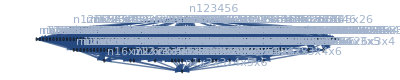

```mathematica
four=Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
IM=IdentityMatrix[Length[VertexList[four]]];
```

```mathematica
fourM=AdjacencyMatrix[four];MatrixForm[fourM]
```

(1)
 |  |  |  |

```mathematica
MakeOne[mat_]:=Map[Map[If[#!=0,1,0]&,#]&, mat]
```

```mathematica
ZetaM=MakeOne[Inverse[IM-fourM]];MatrixForm[ZetaM]
```

(1)
 |  |  |  |

```mathematica
MobiusM=Inverse[ZetaM];MatrixForm[MobiusM,TableHeadings->{VertexList[four],Map[Rotate[#,-Pi/2]&, VertexList[four]]}]
```

(1)
 |  |  |  |

```mathematica
Det[MobiusM]
```

1

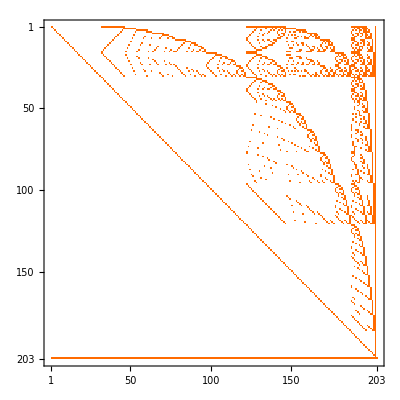

```mathematica
MatrixPlot[ZetaM]
```

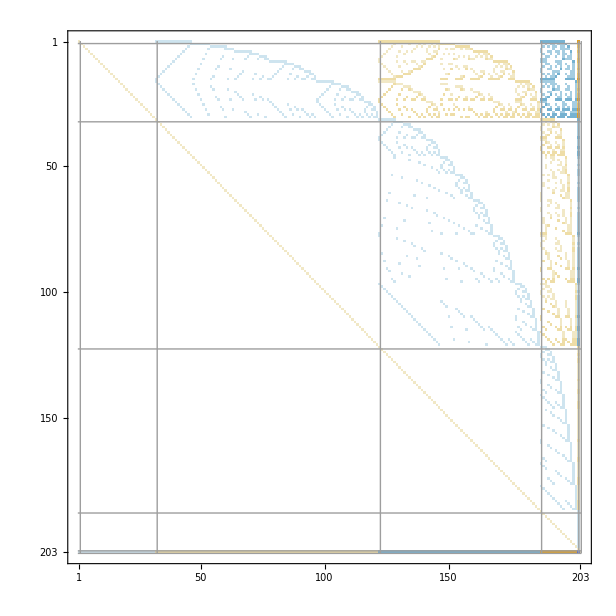

```mathematica
MatrixPlot[MobiusM,Mesh->{Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}],Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}]}]
```

```mathematica
Mob=Association[]
```

<||>

```mathematica
Length[VertexList[four]]
```

203

```mathematica
MobiusM[[203,1]]
```

-1

```mathematica
With[{l=VertexList[four]},
Table[Mob[l[[k]]]=MobiusM[[Length[l],k]],{k,1,Length[l]}]
]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,-120,1}

```mathematica
Gr=Association[];With[{l=VertexList[four]},
Table[Gr[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]],"vertexsets"],{k,1,Length[l]}]
]
```

{{{1},{2,3,4,5,6}},{{1,6},{2,3,4,5}},{{1,5},{2,3,4,6}},{{1,5,6},{2,3,4}},{{1,4},{2,3,5,6}},{{1,4,6},{2,3,5}},{{1,4,5},{2,3,6}},{{1,4,5,6},{2,3}},{{1,3},{2,4,5,6}},{{1,3,6},{2,4,5}},{{1,3,5},{2,4,6}},{{1,3,5,6},{2,4}},{{1,3,4},{2,5,6}},{{1,3,4,6},{2,5}},{{1,3,4,5},{2,6}},{{1,3,4,5,6},{2}},{{1,2},{3,4,5,6}},{{1,2,6},{3,4,5}},{{1,2,5},{3,4,6}},{{1,2,5,6},{3,4}},{{1,2,4},{3,5,6}},{{1,2,4,6},{3,5}},{{1,2,4,5},{3,6}},{{1,2,4,5,6},{3}},{{1,2,3},{4,5,6}},{{1,2,3,6},{4,5}},{{1,2,3,5},{4,6}},{{1,2,3,5,6},{4}},{{1,2,3,4},{5,6}},{{1,2,3,4,6},{5}},{{1,2,3,4,5},{6}},{{1},{2},{3,4,5,6}},{{1},{2,6},{3,4,5}},{{1},{2,5},{3,4,6}},{{1},{2,5,6},{3,4}},{{1},{2,4},{3,5,6}},{{1},{2,4,6},{3,5}},{{1},{2,4,5},{3,6}},{{1},{2,4,5,6},{3}},{{1},{2,3},{4,5,6}},{{1},{2,3,6},{4,5}},{{1},{2,3,5},{4,6}},{{1},{2,3,5,6},{4}},{{1},{2,3,4},{5,6}},{{1},{2,3,4,6},{5}},{{1},{2,3,4,5},{6}},{{1,6},{2},{3,4,5}},{{1,6},{2,5},{3,4}},{{1,6},{2,4},{3,5}},{{1,6},{2,4,5},{3}},{{1,6},{2,3},{4,5}},{{1,6},{2,3,5},{4}},{{1,6},{2,3,4},{5}},{{1,5},{2},{3,4,6}},{{1,5},{2,6},{3,4}},{{1,5},{2,4},{3,6}},{{1,5},{2,4,6},{3}},{{1,5},{2,3},{4,6}},{{1,5},{2,3,6},{4}},{{1,5},{2,3,4},{6}},{{1,5,6},{2},{3,4}},{{1,5,6},{2,4},{3}},{{1,5,6},{2,3},{4}},{{1,4},{2},{3,5,6}},{{1,4},{2,6},{3,5}},{{1,4},{2,5},{3,6}},{{1,4},{2,5,6},{3}},{{1,4},{2,3},{5,6}},{{1,4},{2,3,6},{5}},{{1,4},{2,3,5},{6}},{{1,4,6},{2},{3,5}},{{1,4,6},{2,5},{3}},{{1,4,6},{2,3},{5}},{{1,4,5},{2},{3,6}},{{1,4,5},{2,6},{3}},{{1,4,5},{2,3},{6}},{{1,4,5,6},{2},{3}},{{1,3},{2},{4,5,6}},{{1,3},{2,6},{4,5}},{{1,3},{2,5},{4,6}},{{1,3},{2,5,6},{4}},{{1,3},{2,4},{5,6}},{{1,3},{2,4,6},{5}},{{1,3},{2,4,5},{6}},{{1,3,6},{2},{4,5}},{{1,3,6},{2,5},{4}},{{1,3,6},{2,4},{5}},{{1,3,5},{2},{4,6}},{{1,3,5},{2,6},{4}},{{1,3,5},{2,4},{6}},{{1,3,5,6},{2},{4}},{{1,3,4},{2},{5,6}},{{1,3,4},{2,6},{5}},{{1,3,4},{2,5},{6}},{{1,3,4,6},{2},{5}},{{1,3,4,5},{2},{6}},{{1,2},{3},{4,5,6}},{{1,2},{3,6},{4,5}},{{1,2},{3,5},{4,6}},{{1,2},{3,5,6},{4}},{{1,2},{3,4},{5,6}},{{1,2},{3,4,6},{5}},{{1,2},{3,4,5},{6}},{{1,2,6},{3},{4,5}},{{1,2,6},{3,5},{4}},{{1,2,6},{3,4},{5}},{{1,2,5},{3},{4,6}},{{1,2,5},{3,6},{4}},{{1,2,5},{3,4},{6}},{{1,2,5,6},{3},{4}},{{1,2,4},{3},{5,6}},{{1,2,4},{3,6},{5}},{{1,2,4},{3,5},{6}},{{1,2,4,6},{3},{5}},{{1,2,4,5},{3},{6}},{{1,2,3},{4},{5,6}},{{1,2,3},{4,6},{5}},{{1,2,3},{4,5},{6}},{{1,2,3,6},{4},{5}},{{1,2,3,5},{4},{6}},{{1,2,3,4},{5},{6}},{{1},{2},{3},{4,5,6}},{{1},{2},{3,6},{4,5}},{{1},{2},{3,5},{4,6}},{{1},{2},{3,5,6},{4}},{{1},{2},{3,4},{5,6}},{{1},{2},{3,4,6},{5}},{{1},{2},{3,4,5},{6}},{{1},{2,6},{3},{4,5}},{{1},{2,6},{3,5},{4}},{{1},{2,6},{3,4},{5}},{{1},{2,5},{3},{4,6}},{{1},{2,5},{3,6},{4}},{{1},{2,5},{3,4},{6}},{{1},{2,5,6},{3},{4}},{{1},{2,4},{3},{5,6}},{{1},{2,4},{3,6},{5}},{{1},{2,4},{3,5},{6}},{{1},{2,4,6},{3},{5}},{{1},{2,4,5},{3},{6}},{{1},{2,3},{4},{5,6}},{{1},{2,3},{4,6},{5}},{{1},{2,3},{4,5},{6}},{{1},{2,3,6},{4},{5}},{{1},{2,3,5},{4},{6}},{{1},{2,3,4},{5},{6}},{{1,6},{2},{3},{4,5}},{{1,6},{2},{3,5},{4}},{{1,6},{2},{3,4},{5}},{{1,6},{2,5},{3},{4}},{{1,6},{2,4},{3},{5}},{{1,6},{2,3},{4},{5}},{{1,5},{2},{3},{4,6}},{{1,5},{2},{3,6},{4}},{{1,5},{2},{3,4},{6}},{{1,5},{2,6},{3},{4}},{{1,5},{2,4},{3},{6}},{{1,5},{2,3},{4},{6}},{{1,5,6},{2},{3},{4}},{{1,4},{2},{3},{5,6}},{{1,4},{2},{3,6},{5}},{{1,4},{2},{3,5},{6}},{{1,4},{2,6},{3},{5}},{{1,4},{2,5},{3},{6}},{{1,4},{2,3},{5},{6}},{{1,4,6},{2},{3},{5}},{{1,4,5},{2},{3},{6}},{{1,3},{2},{4},{5,6}},{{1,3},{2},{4,6},{5}},{{1,3},{2},{4,5},{6}},{{1,3},{2,6},{4},{5}},{{1,3},{2,5},{4},{6}},{{1,3},{2,4},{5},{6}},{{1,3,6},{2},{4},{5}},{{1,3,5},{2},{4},{6}},{{1,3,4},{2},{5},{6}},{{1,2},{3},{4},{5,6}},{{1,2},{3},{4,6},{5}},{{1,2},{3},{4,5},{6}},{{1,2},{3,6},{4},{5}},{{1,2},{3,5},{4},{6}},{{1,2},{3,4},{5},{6}},{{1,2,6},{3},{4},{5}},{{1,2,5},{3},{4},{6}},{{1,2,4},{3},{5},{6}},{{1,2,3},{4},{5},{6}},{{1},{2},{3},{4},{5,6}},{{1},{2},{3},{4,6},{5}},{{1},{2},{3},{4,5},{6}},{{1},{2},{3,6},{4},{5}},{{1},{2},{3,5},{4},{6}},{{1},{2},{3,4},{5},{6}},{{1},{2,6},{3},{4},{5}},{{1},{2,5},{3},{4},{6}},{{1},{2,4},{3},{5},{6}},{{1},{2,3},{4},{5},{6}},{{1,6},{2},{3},{4},{5}},{{1,5},{2},{3},{4},{6}},{{1,4},{2},{3},{5},{6}},{{1,3},{2},{4},{5},{6}},{{1,2},{3},{4},{5},{6}},{{1},{2},{3},{4},{5},{6}},{{1,2,3,4,5,6}}}

```mathematica
Gr2=Association[];With[{l=VertexList[four]},
Table[Gr2[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]]],{k,1,Length[l]}]
];
```

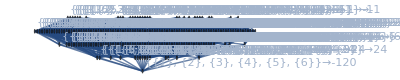

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Rotate[ToString[Gr[v]],Pi/4]->Mob[v],{v,VertexList[four]}],GraphLayout->"LayeredDigraphEmbedding",DirectedEdges->False]
```

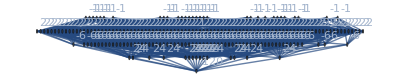

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Mob[v],{v,VertexList[four]}],GraphLayout->"LayeredDigraphEmbedding",DirectedEdges->False]
```

```mathematica
Take[Table[{Gr2[v,"graph"],v,Gr[v],Mob[v],4^Length[Gr[v]],FactorInteger[Mob[v]*4^Length[Gr[v]]]},{v,VertexList[four]}],3]
```

{{-Graphics-,n1x23456,{{1},{2,3,4,5,6}},-1,16,{{-1,1},{2,4}}},{-Graphics-,n16x2345,{{1,6},{2,3,4,5}},-1,16,{{-1,1},{2,4}}},{-Graphics-,n15x2346,{{1,5},{2,3,4,6}},-1,16,{{-1,1},{2,4}}}}

```mathematica
TableForm[Sort[Table[{Gr2[v,"graph"],v,Gr[v],Mob[v],4^Length[Gr[v]],Mob[v]*4^Length[Gr[v]],FactorInteger[Mob[v]*4^Length[Gr[v]]]},{v,VertexList[four]}],Abs[#1[[4]]]>Abs[#2[[4]]]&],TableDepth->2]
```

-Graphics- | n1x2x3x4x5x6 | {{1},{2},{3},{4},{5},{6}} | -120 | 4096 | -491520 | {{-1,1},{2,15},{3,1},{5,1}}
-Graphics- | n12x3x4x5x6 | {{1,2},{3},{4},{5},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n13x2x4x5x6 | {{1,3},{2},{4},{5},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n14x2x3x5x6 | {{1,4},{2},{3},{5},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n15x2x3x4x6 | {{1,5},{2},{3},{4},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n16x2x3x4x5 | {{1,6},{2},{3},{4},{5}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x23x4x5x6 | {{1},{2,3},{4},{5},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x24x3x5x6 | {{1},{2,4},{3},{5},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x25x3x4x6 | {{1},{2,5},{3},{4},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x26x3x4x5 | {{1},{2,6},{3},{4},{5}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x2x34x5x6 | {{1},{2},{3,4},{5},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x2x35x4x6 | {{1},{2},{3,5},{4},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x2x36x4x5 | {{1},{2},{3,6},{4},{5}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x2x3x45x6 | {{1},{2},{3},{4,5},{6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x2x3x46x5 | {{1},{2},{3},{4,6},{5}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n1x2x3x4x56 | {{1},{2},{3},{4},{5,6}} | 24 | 1024 | 24576 | {{2,13},{3,1}}
-Graphics- | n123x4x5x6 | {{1,2,3},{4},{5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n124x3x5x6 | {{1,2,4},{3},{5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n125x3x4x6 | {{1,2,5},{3},{4},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n126x3x4x5 | {{1,2,6},{3},{4},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n12x34x5x6 | {{1,2},{3,4},{5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n12x35x4x6 | {{1,2},{3,5},{4},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n12x36x4x5 | {{1,2},{3,6},{4},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n12x3x45x6 | {{1,2},{3},{4,5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n12x3x46x5 | {{1,2},{3},{4,6},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n12x3x4x56 | {{1,2},{3},{4},{5,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n134x2x5x6 | {{1,3,4},{2},{5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n135x2x4x6 | {{1,3,5},{2},{4},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n136x2x4x5 | {{1,3,6},{2},{4},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n13x24x5x6 | {{1,3},{2,4},{5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n13x25x4x6 | {{1,3},{2,5},{4},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n13x26x4x5 | {{1,3},{2,6},{4},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n13x2x45x6 | {{1,3},{2},{4,5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n13x2x46x5 | {{1,3},{2},{4,6},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n13x2x4x56 | {{1,3},{2},{4},{5,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n145x2x3x6 | {{1,4,5},{2},{3},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n146x2x3x5 | {{1,4,6},{2},{3},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n14x23x5x6 | {{1,4},{2,3},{5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n14x25x3x6 | {{1,4},{2,5},{3},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n14x26x3x5 | {{1,4},{2,6},{3},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n14x2x35x6 | {{1,4},{2},{3,5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n14x2x36x5 | {{1,4},{2},{3,6},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n14x2x3x56 | {{1,4},{2},{3},{5,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n156x2x3x4 | {{1,5,6},{2},{3},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n15x23x4x6 | {{1,5},{2,3},{4},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n15x24x3x6 | {{1,5},{2,4},{3},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n15x26x3x4 | {{1,5},{2,6},{3},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n15x2x34x6 | {{1,5},{2},{3,4},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n15x2x36x4 | {{1,5},{2},{3,6},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n15x2x3x46 | {{1,5},{2},{3},{4,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n16x23x4x5 | {{1,6},{2,3},{4},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n16x24x3x5 | {{1,6},{2,4},{3},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n16x25x3x4 | {{1,6},{2,5},{3},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n16x2x34x5 | {{1,6},{2},{3,4},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n16x2x35x4 | {{1,6},{2},{3,5},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n16x2x3x45 | {{1,6},{2},{3},{4,5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x234x5x6 | {{1},{2,3,4},{5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x235x4x6 | {{1},{2,3,5},{4},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x236x4x5 | {{1},{2,3,6},{4},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x23x45x6 | {{1},{2,3},{4,5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x23x46x5 | {{1},{2,3},{4,6},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x23x4x56 | {{1},{2,3},{4},{5,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x245x3x6 | {{1},{2,4,5},{3},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x246x3x5 | {{1},{2,4,6},{3},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x24x35x6 | {{1},{2,4},{3,5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x24x36x5 | {{1},{2,4},{3,6},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x24x3x56 | {{1},{2,4},{3},{5,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x256x3x4 | {{1},{2,5,6},{3},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x25x34x6 | {{1},{2,5},{3,4},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x25x36x4 | {{1},{2,5},{3,6},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x25x3x46 | {{1},{2,5},{3},{4,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x26x34x5 | {{1},{2,6},{3,4},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x26x35x4 | {{1},{2,6},{3,5},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x26x3x45 | {{1},{2,6},{3},{4,5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x2x345x6 | {{1},{2},{3,4,5},{6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x2x346x5 | {{1},{2},{3,4,6},{5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x2x34x56 | {{1},{2},{3,4},{5,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x2x356x4 | {{1},{2},{3,5,6},{4}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x2x35x46 | {{1},{2},{3,5},{4,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x2x36x45 | {{1},{2},{3,6},{4,5}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1x2x3x456 | {{1},{2},{3},{4,5,6}} | -6 | 256 | -1536 | {{-1,1},{2,9},{3,1}}
-Graphics- | n1234x5x6 | {{1,2,3,4},{5},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1235x4x6 | {{1,2,3,5},{4},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1236x4x5 | {{1,2,3,6},{4},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n123x45x6 | {{1,2,3},{4,5},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n123x46x5 | {{1,2,3},{4,6},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n123x4x56 | {{1,2,3},{4},{5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1245x3x6 | {{1,2,4,5},{3},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1246x3x5 | {{1,2,4,6},{3},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n124x35x6 | {{1,2,4},{3,5},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n124x36x5 | {{1,2,4},{3,6},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n124x3x56 | {{1,2,4},{3},{5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1256x3x4 | {{1,2,5,6},{3},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n125x34x6 | {{1,2,5},{3,4},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n125x36x4 | {{1,2,5},{3,6},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n125x3x46 | {{1,2,5},{3},{4,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n126x34x5 | {{1,2,6},{3,4},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n126x35x4 | {{1,2,6},{3,5},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n126x3x45 | {{1,2,6},{3},{4,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n12x345x6 | {{1,2},{3,4,5},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n12x346x5 | {{1,2},{3,4,6},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n12x34x56 | {{1,2},{3,4},{5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n12x356x4 | {{1,2},{3,5,6},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n12x35x46 | {{1,2},{3,5},{4,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n12x36x45 | {{1,2},{3,6},{4,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n12x3x456 | {{1,2},{3},{4,5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1345x2x6 | {{1,3,4,5},{2},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1346x2x5 | {{1,3,4,6},{2},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n134x25x6 | {{1,3,4},{2,5},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n134x26x5 | {{1,3,4},{2,6},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n134x2x56 | {{1,3,4},{2},{5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1356x2x4 | {{1,3,5,6},{2},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n135x24x6 | {{1,3,5},{2,4},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n135x26x4 | {{1,3,5},{2,6},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n135x2x46 | {{1,3,5},{2},{4,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n136x24x5 | {{1,3,6},{2,4},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n136x25x4 | {{1,3,6},{2,5},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n136x2x45 | {{1,3,6},{2},{4,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n13x245x6 | {{1,3},{2,4,5},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n13x246x5 | {{1,3},{2,4,6},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n13x24x56 | {{1,3},{2,4},{5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n13x256x4 | {{1,3},{2,5,6},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n13x25x46 | {{1,3},{2,5},{4,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n13x26x45 | {{1,3},{2,6},{4,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n13x2x456 | {{1,3},{2},{4,5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1456x2x3 | {{1,4,5,6},{2},{3}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n145x23x6 | {{1,4,5},{2,3},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n145x26x3 | {{1,4,5},{2,6},{3}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n145x2x36 | {{1,4,5},{2},{3,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n146x23x5 | {{1,4,6},{2,3},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n146x25x3 | {{1,4,6},{2,5},{3}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n146x2x35 | {{1,4,6},{2},{3,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n14x235x6 | {{1,4},{2,3,5},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n14x236x5 | {{1,4},{2,3,6},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n14x23x56 | {{1,4},{2,3},{5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n14x256x3 | {{1,4},{2,5,6},{3}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n14x25x36 | {{1,4},{2,5},{3,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n14x26x35 | {{1,4},{2,6},{3,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n14x2x356 | {{1,4},{2},{3,5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n156x23x4 | {{1,5,6},{2,3},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n156x24x3 | {{1,5,6},{2,4},{3}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n156x2x34 | {{1,5,6},{2},{3,4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n15x234x6 | {{1,5},{2,3,4},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n15x236x4 | {{1,5},{2,3,6},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n15x23x46 | {{1,5},{2,3},{4,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n15x246x3 | {{1,5},{2,4,6},{3}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n15x24x36 | {{1,5},{2,4},{3,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n15x26x34 | {{1,5},{2,6},{3,4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n15x2x346 | {{1,5},{2},{3,4,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n16x234x5 | {{1,6},{2,3,4},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n16x235x4 | {{1,6},{2,3,5},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n16x23x45 | {{1,6},{2,3},{4,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n16x245x3 | {{1,6},{2,4,5},{3}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n16x24x35 | {{1,6},{2,4},{3,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n16x25x34 | {{1,6},{2,5},{3,4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n16x2x345 | {{1,6},{2},{3,4,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x2345x6 | {{1},{2,3,4,5},{6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x2346x5 | {{1},{2,3,4,6},{5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x234x56 | {{1},{2,3,4},{5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x2356x4 | {{1},{2,3,5,6},{4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x235x46 | {{1},{2,3,5},{4,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x236x45 | {{1},{2,3,6},{4,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x23x456 | {{1},{2,3},{4,5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x2456x3 | {{1},{2,4,5,6},{3}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x245x36 | {{1},{2,4,5},{3,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x246x35 | {{1},{2,4,6},{3,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x24x356 | {{1},{2,4},{3,5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x256x34 | {{1},{2,5,6},{3,4}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x25x346 | {{1},{2,5},{3,4,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x26x345 | {{1},{2,6},{3,4,5}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n1x2x3456 | {{1},{2},{3,4,5,6}} | 2 | 64 | 128 | {{2,7}}
-Graphics- | n123456 | {{1,2,3,4,5,6}} | 1 | 4 | 4 | {{2,2}}
-Graphics- | n12345x6 | {{1,2,3,4,5},{6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n12346x5 | {{1,2,3,4,6},{5}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1234x56 | {{1,2,3,4},{5,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n12356x4 | {{1,2,3,5,6},{4}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1235x46 | {{1,2,3,5},{4,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1236x45 | {{1,2,3,6},{4,5}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n123x456 | {{1,2,3},{4,5,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n12456x3 | {{1,2,4,5,6},{3}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1245x36 | {{1,2,4,5},{3,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1246x35 | {{1,2,4,6},{3,5}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n124x356 | {{1,2,4},{3,5,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1256x34 | {{1,2,5,6},{3,4}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n125x346 | {{1,2,5},{3,4,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n126x345 | {{1,2,6},{3,4,5}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n12x3456 | {{1,2},{3,4,5,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n13456x2 | {{1,3,4,5,6},{2}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1345x26 | {{1,3,4,5},{2,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1346x25 | {{1,3,4,6},{2,5}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n134x256 | {{1,3,4},{2,5,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1356x24 | {{1,3,5,6},{2,4}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n135x246 | {{1,3,5},{2,4,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n136x245 | {{1,3,6},{2,4,5}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n13x2456 | {{1,3},{2,4,5,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1456x23 | {{1,4,5,6},{2,3}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n145x236 | {{1,4,5},{2,3,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n146x235 | {{1,4,6},{2,3,5}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n14x2356 | {{1,4},{2,3,5,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n156x234 | {{1,5,6},{2,3,4}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n15x2346 | {{1,5},{2,3,4,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n16x2345 | {{1,6},{2,3,4,5}} | -1 | 16 | -16 | {{-1,1},{2,4}}
-Graphics- | n1x23456 | {{1},{2,3,4,5,6}} | -1 | 16 | -16 | {{-1,1},{2,4}}

```mathematica
ZetaM//MatrixPlot
```

-Graphics-

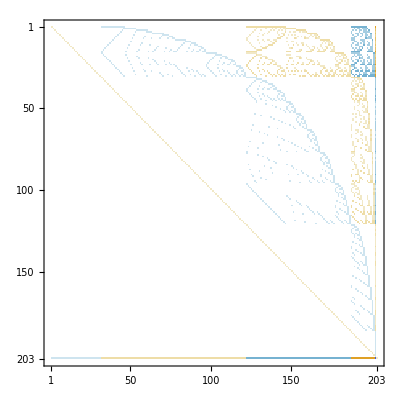

```mathematica
Inverse[ZetaM]//MatrixPlot
```

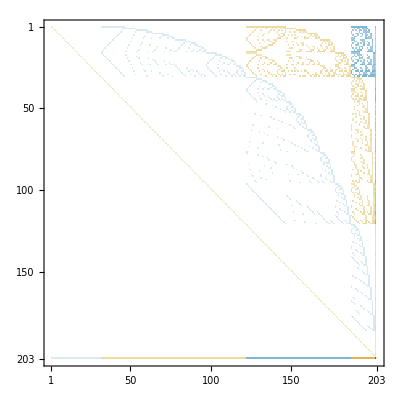

```mathematica
MatrixPower[Inverse[ZetaM],3]//MatrixPlot
```

```mathematica
MatrixPower[Inverse[ZetaM],15]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
Subgraph
```

Subgraph

```mathematica
GraphZeta[g_]:=Block[{ordered=TopologicalSort[four]},
Table[If[ToString[i]==ToString[j]||EdgeQ[g,i->j],1,0],{i,ordered},{j,ordered}]
]
```

```mathematica
GraphZeta[four]//MatrixForm
```

(1)
 |  |  |  |

```mathematica
Inverse[GraphZeta[four]]//MatrixForm
```

(1)
 |  |  |  |

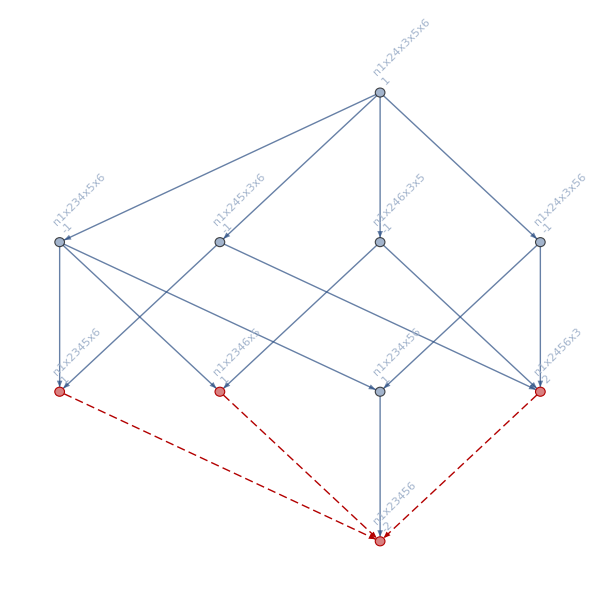
-Graphics-→-Graphics-

```mathematica
allGraphs[alfaKey,"graph"]->With[
{g=Graph[Join[Flatten[Table[EdgeList[ MobiusGraph[k]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]]]},
Graph[MobiusGraph[alfaKey],GraphHighlight->Join[VertexList[g],EdgeList[g]],GraphHighlightStyle->"Dashed"]
]
```

```mathematica
repPoly=Table[allGraphs[k,"colofourrealnull"]->ChromaticPolynomial[allGraphs[k,"graph"],x],{k,realyNullAtomKeys}]
```

{n1x2x3x4x5x6→x^6,n12x3x4x5x6→x^5,n123x4x5x6→x^4,n1234x5x6→x^3,n12345x6→x^2,n123456→x,n12346x5→x^2,n1234x56→x^2,n1235x4x6→x^3,n12356x4→x^2,n1235x46→x^2,n1236x4x5→x^3,n1236x45→x^2,n123x45x6→x^3,n123x456→x^2,n123x46x5→x^3,n123x4x56→x^3,n124x3x5x6→x^4,n1245x3x6→x^3,n12456x3→x^2,n1245x36→x^2,n1246x3x5→x^3,n1246x35→x^2,n124x35x6→x^3,n124x356→x^2,n124x36x5→x^3,n124x3x56→x^3,n125x3x4x6→x^4,n1256x3x4→x^3,n1256x34→x^2,n125x34x6→x^3,n125x346→x^2,n125x36x4→x^3,n125x3x46→x^3,n126x3x4x5→x^4,n126x34x5→x^3,n126x345→x^2,n126x35x4→x^3,n126x3x45→x^3,n12x34x5x6→x^4,n12x345x6→x^3,n12x3456→x^2,n12x346x5→x^3,n12x34x56→x^3,n12x35x4x6→x^4,n12x356x4→x^3,n12x35x46→x^3,n12x36x4x5→x^4,n12x36x45→x^3,n12x3x45x6→x^4,n12x3x456→x^3,n12x3x46x5→x^4,n12x3x4x56→x^4,n13x2x4x5x6→x^5,n134x2x5x6→x^4,n1345x2x6→x^3,n13456x2→x^2,n1345x26→x^2,n1346x2x5→x^3,n1346x25→x^2,n134x25x6→x^3,n134x256→x^2,n134x26x5→x^3,n134x2x56→x^3,n135x2x4x6→x^4,n1356x2x4→x^3,n1356x24→x^2,n135x24x6→x^3,n135x246→x^2,n135x26x4→x^3,n135x2x46→x^3,n136x2x4x5→x^4,n136x24x5→x^3,n136x245→x^2,n136x25x4→x^3,n136x2x45→x^3,n13x24x5x6→x^4,n13x245x6→x^3,n13x2456→x^2,n13x246x5→x^3,n13x24x56→x^3,n13x25x4x6→x^4,n13x256x4→x^3,n13x25x46→x^3,n13x26x4x5→x^4,n13x26x45→x^3,n13x2x45x6→x^4,n13x2x456→x^3,n13x2x46x5→x^4,n13x2x4x56→x^4,n14x2x3x5x6→x^5,n145x2x3x6→x^4,n1456x2x3→x^3,n1456x23→x^2,n145x23x6→x^3,n145x236→x^2,n145x26x3→x^3,n145x2x36→x^3,n146x2x3x5→x^4,n146x23x5→x^3,n146x235→x^2,n146x25x3→x^3,n146x2x35→x^3,n14x23x5x6→x^4,n14x235x6→x^3,n14x2356→x^2,n14x236x5→x^3,n14x23x56→x^3,n14x25x3x6→x^4,n14x256x3→x^3,n14x25x36→x^3,n14x26x3x5→x^4,n14x26x35→x^3,n14x2x35x6→x^4,n14x2x356→x^3,n14x2x36x5→x^4,n14x2x3x56→x^4,n15x2x3x4x6→x^5,n156x2x3x4→x^4,n156x23x4→x^3,n156x234→x^2,n156x24x3→x^3,n156x2x34→x^3,n15x23x4x6→x^4,n15x234x6→x^3,n15x2346→x^2,n15x236x4→x^3,n15x23x46→x^3,n15x24x3x6→x^4,n15x246x3→x^3,n15x24x36→x^3,n15x26x3x4→x^4,n15x26x34→x^3,n15x2x34x6→x^4,n15x2x346→x^3,n15x2x36x4→x^4,n15x2x3x46→x^4,n16x2x3x4x5→x^5,n16x23x4x5→x^4,n16x234x5→x^3,n16x2345→x^2,n16x235x4→x^3,n16x23x45→x^3,n16x24x3x5→x^4,n16x245x3→x^3,n16x24x35→x^3,n16x25x3x4→x^4,n16x25x34→x^3,n16x2x34x5→x^4,n16x2x345→x^3,n16x2x35x4→x^4,n16x2x3x45→x^4,n1x23x4x5x6→x^5,n1x234x5x6→x^4,n1x2345x6→x^3,n1x23456→x^2,n1x2346x5→x^3,n1x234x56→x^3,n1x235x4x6→x^4,n1x2356x4→x^3,n1x235x46→x^3,n1x236x4x5→x^4,n1x236x45→x^3,n1x23x45x6→x^4,n1x23x456→x^3,n1x23x46x5→x^4,n1x23x4x56→x^4,n1x24x3x5x6→x^5,n1x245x3x6→x^4,n1x2456x3→x^3,n1x245x36→x^3,n1x246x3x5→x^4,n1x246x35→x^3,n1x24x35x6→x^4,n1x24x356→x^3,n1x24x36x5→x^4,n1x24x3x56→x^4,n1x25x3x4x6→x^5,n1x256x3x4→x^4,n1x256x34→x^3,n1x25x34x6→x^4,n1x25x346→x^3,n1x25x36x4→x^4,n1x25x3x46→x^4,n1x26x3x4x5→x^5,n1x26x34x5→x^4,n1x26x345→x^3,n1x26x35x4→x^4,n1x26x3x45→x^4,n1x2x34x5x6→x^5,n1x2x345x6→x^4,n1x2x3456→x^3,n1x2x346x5→x^4,n1x2x34x56→x^4,n1x2x35x4x6→x^5,n1x2x356x4→x^4,n1x2x35x46→x^4,n1x2x36x4x5→x^5,n1x2x36x45→x^4,n1x2x3x45x6→x^5,n1x2x3x456→x^4,n1x2x3x46x5→x^5,n1x2x3x4x56→x^5}

```mathematica
allGraphs[k6Key,"colofourrealnull"]/.repPoly
```

Missing[KeyAbsent,k6Key]

```mathematica
ChromaticPolynomial[allGraphs[k6Key,"graph"],x]
```

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[Missing[KeyAbsent,k6Key],x].

ChromaticPolynomial[Missing[KeyAbsent,k6Key],x]

```mathematica
AssociationToList[a_]:=Table[{k,a[k]//Total,a[k]//Length,a[k]//Tally//Sort},{k,Keys[a]}]
```

```mathematica
TableForm[AssociationToList[MobiusTable [k6Key]]//Sort, TableDepth->2]
```

SymbolName::sym: Argument Missing[KeyAbsent,k6Key] at position 1 is expected to be a symbol.

StringCount::strse: String or list of strings expected at position 1 in StringCount[SymbolName[Missing[KeyAbsent,k6Key]],x].

StringCount[SymbolName[Missing[KeyAbsent,k6Key]],x] | 1 | 1 | {{1,1}}

```mathematica
ChromaticPolynomial[CompleteGraph[6],x]
```

-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6

```mathematica
CompleteBaseCoeff[ChromaticPolynomial[CompleteGraph[6],x]]
```

{0,0,0,0,0,0,1}

```mathematica
TableForm[AssociationToList[MobiusTable [k5Key]]//Sort, TableDepth->2]
```

1 | 24 | 1 | {{24,1}}
2 | -50 | 15 | {{-6,5},{-2,10}}
3 | 35 | 25 | {{1,15},{2,10}}
4 | -10 | 10 | {{-1,10}}
5 | 1 | 1 | {{1,1}}

```mathematica
Table[StirlingS2[6,k],{k,0,6}]
```

{0,1,31,90,65,15,1}

```mathematica
fullVars6=Map[Symbol[StringJoin["v",StringDrop[SymbolName[#],1]]]&,VertexList[four]]
```

{v1x23456,v16x2345,v15x2346,v156x234,v14x2356,v146x235,v145x236,v1456x23,v13x2456,v136x245,v135x246,v1356x24,v134x256,v1346x25,v1345x26,v13456x2,v12x3456,v126x345,v125x346,v1256x34,v124x356,v1246x35,v1245x36,v12456x3,v123x456,v1236x45,v1235x46,v12356x4,v1234x56,v12346x5,v12345x6,v1x2x3456,v1x26x345,v1x25x346,v1x256x34,v1x24x356,v1x246x35,v1x245x36,v1x2456x3,v1x23x456,v1x236x45,v1x235x46,v1x2356x4,v1x234x56,v1x2346x5,v1x2345x6,v16x2x345,v16x25x34,v16x24x35,v16x245x3,v16x23x45,v16x235x4,v16x234x5,v15x2x346,v15x26x34,v15x24x36,v15x246x3,v15x23x46,v15x236x4,v15x234x6,v156x2x34,v156x24x3,v156x23x4,v14x2x356,v14x26x35,v14x25x36,v14x256x3,v14x23x56,v14x236x5,v14x235x6,v146x2x35,v146x25x3,v146x23x5,v145x2x36,v145x26x3,v145x23x6,v1456x2x3,v13x2x456,v13x26x45,v13x25x46,v13x256x4,v13x24x56,v13x246x5,v13x245x6,v136x2x45,v136x25x4,v136x24x5,v135x2x46,v135x26x4,v135x24x6,v1356x2x4,v134x2x56,v134x26x5,v134x25x6,v1346x2x5,v1345x2x6,v12x3x456,v12x36x45,v12x35x46,v12x356x4,v12x34x56,v12x346x5,v12x345x6,v126x3x45,v126x35x4,v126x34x5,v125x3x46,v125x36x4,v125x34x6,v1256x3x4,v124x3x56,v124x36x5,v124x35x6,v1246x3x5,v1245x3x6,v123x4x56,v123x46x5,v123x45x6,v1236x4x5,v1235x4x6,v1234x5x6,v1x2x3x456,v1x2x36x45,v1x2x35x46,v1x2x356x4,v1x2x34x56,v1x2x346x5,v1x2x345x6,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x256x3x4,v1x24x3x56,v1x24x36x5,v1x24x35x6,v1x246x3x5,v1x245x3x6,v1x23x4x56,v1x23x46x5,v1x23x45x6,v1x236x4x5,v1x235x4x6,v1x234x5x6,v16x2x3x45,v16x2x35x4,v16x2x34x5,v16x25x3x4,v16x24x3x5,v16x23x4x5,v15x2x3x46,v15x2x36x4,v15x2x34x6,v15x26x3x4,v15x24x3x6,v15x23x4x6,v156x2x3x4,v14x2x3x56,v14x2x36x5,v14x2x35x6,v14x26x3x5,v14x25x3x6,v14x23x5x6,v146x2x3x5,v145x2x3x6,v13x2x4x56,v13x2x46x5,v13x2x45x6,v13x26x4x5,v13x25x4x6,v13x24x5x6,v136x2x4x5,v135x2x4x6,v134x2x5x6,v12x3x4x56,v12x3x46x5,v12x3x45x6,v12x36x4x5,v12x35x4x6,v12x34x5x6,v126x3x4x5,v125x3x4x6,v124x3x5x6,v123x4x5x6,v1x2x3x4x56,v1x2x3x46x5,v1x2x3x45x6,v1x2x36x4x5,v1x2x35x4x6,v1x2x34x5x6,v1x26x3x4x5,v1x25x3x4x6,v1x24x3x5x6,v1x23x4x5x6,v16x2x3x4x5,v15x2x3x4x6,v14x2x3x5x6,v13x2x4x5x6,v12x3x4x5x6,v1x2x3x4x5x6,v123456}

```mathematica
CompactMobius6[]:=Block[{result,i,j,a,b},
result=Table[0,{k,1,6},{l,1,6}];
a=1;
Table[
b=1;
Table[
i=StringCount[SymbolName[row],"x"]+1;
j=StringCount[SymbolName[col],"x"]+1;
result[[i,j]]+=ZetaM[[a,b]];
(*result[[j,i]]+=ZetaM[[a,b]];*)
b++;
,
{col,fullVars6}
];
a++,
{row,fullVars6}
];
result
]
```

```mathematica
CompactMobius6[]//MatrixForm
```

(1 | 31 | 90 | 65 | 15 | 1
0 | 31 | 270 | 455 | 225 | 31
0 | 0 | 90 | 390 | 375 | 90
0 | 0 | 0 | 65 | 150 | 65
0 | 0 | 0 | 0 | 15 | 15
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Table[StirlingS2[j,i]*StirlingS2[6,i],{i,1,6},{j,1,6}]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1
0 | 31 | 93 | 217 | 465 | 961
0 | 0 | 90 | 540 | 2250 | 8100
0 | 0 | 0 | 65 | 650 | 4225
0 | 0 | 0 | 0 | 15 | 225
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Table[StirlingS2[j,i]*StirlingS2[6,j],{i,1,6},{j,1,6}]//MatrixForm
```

(1 | 31 | 90 | 65 | 15 | 1
0 | 31 | 270 | 455 | 225 | 31
0 | 0 | 90 | 390 | 375 | 90
0 | 0 | 0 | 65 | 150 | 65
0 | 0 | 0 | 0 | 15 | 15
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
455/65
```

7

```mathematica
6*65
```

390

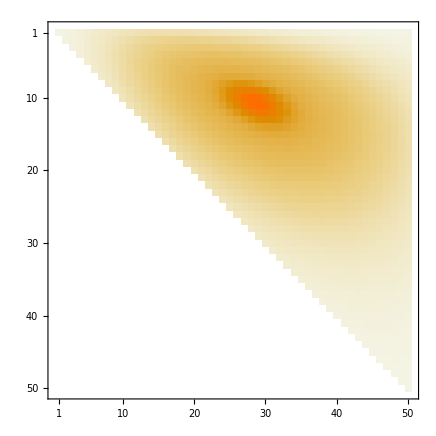

```mathematica
Table[StirlingS2[j,i]*StirlingS2[50,j],{i,1,50},{j,1,50}]//MatrixPlot
```